```mathematica
f[x_,y_]=10^4 TriangleWave[6Max[Abs[√x-0.5],Abs[y^2-0.5]]];
Ω=Region[Rectangle[{0,0},{1,1}]];
U[x_,y_]=NDSolveValue[
{∇_{x,y}^2 u[x,y]==f[x,y],
DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Ω];
ContourPlot[U[x,y],{x,0,1},{y,0,1},PlotLegends->Automatic,PlotPoints->100,Contours->20,PlotRange->All]
ContourPlot[f[x,y],{x,0,1},{y,0,1},PlotLegends->Automatic,PlotPoints->50]
U[.5,.5]
```

-Graphics-

-Graphics-

30.3186

InterpolatingFunction[{{-3., 3.}, {-2., 2.}}, <>][x,y]

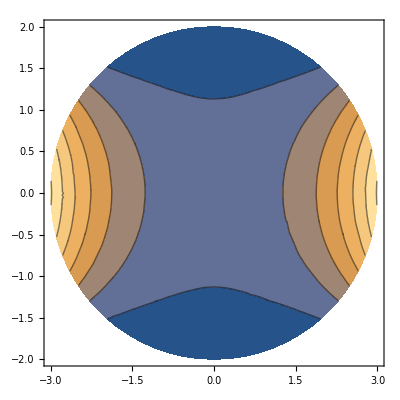

```mathematica
a=3;
b=2;
Ω=Region[Ellipsoid[{0,0},{a,b}]];
U[x_,y_]=NDSolveValue[
{∇_{x,y}^2 u[x,y]==1,
DirichletCondition[u[x,y]==x^4+y^4,True]},
u[x,y],{x,y}∈Ω,AccuracyGoal->30]
ContourPlot[U[x,y],{x,y}∈Ω]
```

x^4+y^4+InterpolatingFunction[{{-3., 3.}, {-2., 2.}}, <>][x,y]

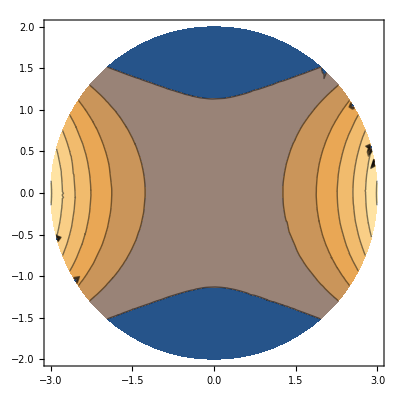

```mathematica
a=3;
b=2;
Ω=Region[Ellipsoid[{0,0},{a,b}]];
UHom[x_,y_]=(x^4+y^4)+NDSolveValue[
{∇_{x,y}^2 v[x,y]==1-12(x^2+y^2),
DirichletCondition[v[x,y]==0,True]},
v[x,y],{x,y}∈Ω,AccuracyGoal->30]
ContourPlot[U[x,y],{x,y}∈Ω]
```

```mathematica
a=3;
b=2;
Ω=Region[Ellipsoid[{0,0},{a,b}]];
ULap[x_,y_]=(x^2+y^2)/4+NDSolveValue[
{∇_{x,y}^2 u[x,y]==0,
DirichletCondition[u[x,y]==x^4-(x^2+y^2)/4+y^4,True]},
u[x,y],{x,y}∈Ω,AccuracyGoal->30]
ContourPlot[U[x,y],{x,y}∈Ω]
```

1/4 (x^2+y^2)+InterpolatingFunction[{{-3., 3.}, {-2., 2.}}, <>][x,y]

-Graphics-

```mathematica
Plot3D[Log[10,Abs[U[x,y]-UHom[x,y]]],{x,y}∈Ω,PlotLegends->Automatic]
Plot3D[Log[10,Abs[U[x,y]-ULap[x,y]]],{x,y}∈Ω,PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-